```mathematica
Import["/home/jacob/SynologyDrive/Universität/QuantenInfo/Bachelorarbeit/RTNI-master/MATHEMATICA/Data/PartialTrace.m"]

Import["/home/jacob/SynologyDrive/Universität/QuantenInfo/Bachelorarbeit/RTNI-master/MATHEMATICA/Data/Circuit_AtoB_1_AnalysCircuitSum.m"]
Import["/home/jacob/SynologyDrive/Universität/QuantenInfo/Bachelorarbeit/RTNI-master/MATHEMATICA/Data/Circuit_AtoB_2_AnalysCircuitSum.m"]
Import["/home/jacob/SynologyDrive/Universität/QuantenInfo/Bachelorarbeit/RTNI-master/MATHEMATICA/Data/Circuit_AtoB_3_AnalysCircuitSum.m"]
Import["/home/jacob/SynologyDrive/Universität/QuantenInfo/Bachelorarbeit/RTNI-master/MATHEMATICA/Data/Circuit_AtoB_4_AnalysCircuitSum.m"]
Import["/home/jacob/SynologyDrive/Universität/QuantenInfo/Bachelorarbeit/RTNI-master/MATHEMATICA/Data/Circuit_AtoB_6_AnalysCircuitSum.m"]
Import["/home/jacob/SynologyDrive/Universität/QuantenInfo/Bachelorarbeit/RTNI-master/MATHEMATICA/Data/Circuit_AtoB_8_AnalysCircuitSum.m"]


Import["/home/jacob/SynologyDrive/Universität/QuantenInfo/Bachelorarbeit/RTNI-master/MATHEMATICA/Data/Circuit_AtoD_1_AnalysCircuitSum.m"]
Import["/home/jacob/SynologyDrive/Universität/QuantenInfo/Bachelorarbeit/RTNI-master/MATHEMATICA/Data/Circuit_AtoD_2_AnalysCircuitSum.m"]
Import["/home/jacob/SynologyDrive/Universität/QuantenInfo/Bachelorarbeit/RTNI-master/MATHEMATICA/Data/Circuit_AtoD_3_AnalysCircuitSum.m"]
Import["/home/jacob/SynologyDrive/Universität/QuantenInfo/Bachelorarbeit/RTNI-master/MATHEMATICA/Data/Circuit_AtoD_4_AnalysCircuitSum.m"]

Import["/home/jacob/SynologyDrive/Universität/QuantenInfo/Bachelorarbeit/RTNI-master/MATHEMATICA/Data/Circuit_AtoF_1_AnalysCircuitSum.m"]
Import["/home/jacob/SynologyDrive/Universität/QuantenInfo/Bachelorarbeit/RTNI-master/MATHEMATICA/Data/Circuit_AtoF_2_AnalysCircuitSum.m"]
Import["/home/jacob/SynologyDrive/Universität/QuantenInfo/Bachelorarbeit/RTNI-master/MATHEMATICA/Data/Circuit_AtoF_3_AnalysCircuitSum.m"]

Import["/home/jacob/SynologyDrive/Universität/QuantenInfo/Bachelorarbeit/RTNI-master/MATHEMATICA/Data/Circuit_AtoH_1_AnalysCircuitSum.m"]
Import["/home/jacob/SynologyDrive/Universität/QuantenInfo/Bachelorarbeit/RTNI-master/MATHEMATICA/Data/Circuit_AtoH_2_AnalysCircuitSum.m"]

A={{1,0},{0,0}};
X=PauliMatrix[1];
Y =PauliMatrix[2];
Z = PauliMatrix[3];
qe1 = (X+Y+Z)/(√3);
eXYZ = MatrixExp[ I α KroneckerProduct[qe1,qe1]];
eZZ = MatrixExp[ I α KroneckerProduct[Z,Z]];
eXX = MatrixExp[ I α KroneckerProduct[X,X]];
(*Plot[{Abs[Tr[eXYZYXZ]],Abs[Tr[eXX]],Abs[Tr[eZZ]]},{α,0,2 Pi}]*)
```

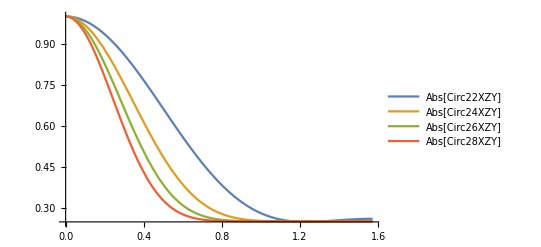

```mathematica
Circ22XZY = Simplify[Refine[CircuitSum2w2d[eXYZ,A],α>0]];
Circ24XZY = Simplify[Refine[CircuitSum2w4d[eXYZ,A],α>0]];
Circ26XZY = Simplify[Refine[CircuitSum2w6d[eXYZ,A],α>0]];
Circ28XZY = Simplify[Refine[CircuitSum2w8d[eXYZ,A],α>0]];
Plot[{Abs[Circ22XZY],Abs[Circ24XZY],Abs[Circ26XZY],Abs[Circ28XZY]},{α,0,Pi/2},PlotRange->All,LabelStyle->Directive[Bold, Medium],PlotLegends->"Expressions"]
```

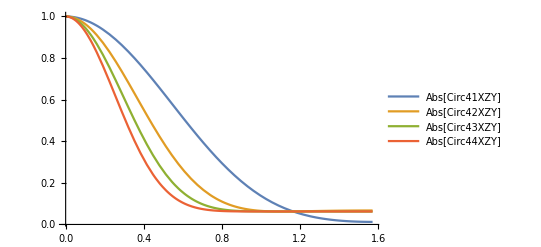

```mathematica
Circ41XZY = Simplify[Refine[CircuitSum4w1d[eXYZ,A],α>0]];
Circ42XZY = Simplify[Refine[CircuitSum4w2d[eXYZ,A],α>0]];
Circ43XZY = Simplify[Refine[CircuitSum4w3d[eXYZ,A],α>0]];
Circ44XZY = Simplify[Refine[CircuitSum4w4d[eXYZ,A],α>0]];
Plot[{Abs[Circ41XZY],Abs[Circ42XZY],Abs[Circ43XZY],Abs[Circ44XZY]},{α,0,Pi/2},PlotRange->All,LabelStyle->Directive[Bold, Medium],PlotLegends->"Expressions"]
```

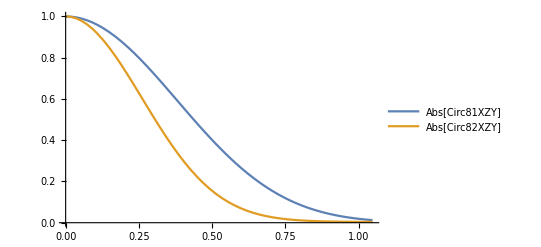

```mathematica
Circ81XZY = Simplify[Refine[CircuitSum8w1d[eXYZ,A],α>0]];
Circ82XZY = Simplify[Refine[CircuitSum8w2d[eXYZ,A],α>0]];
Plot[{Abs[Circ81XZY],Abs[Circ82XZY]},{α,0,Pi/3},PlotRange->All,LabelStyle->Directive[Bold, Medium],PlotLegends->"Expressions"]
```

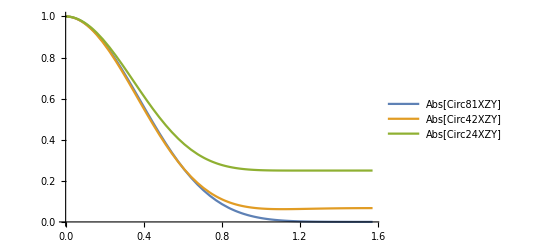

```mathematica
Plot[{Abs[Circ81XZY],Abs[Circ42XZY],Abs[Circ24XZY]},{α,0,Pi/2},PlotRange->All,LabelStyle->Directive[Bold, Medium],PlotLegends->"Expressions"]
```

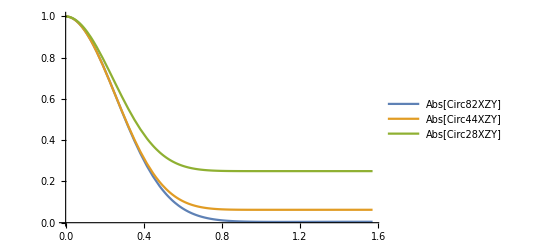

```mathematica
Plot[{Abs[Circ82XZY],Abs[Circ44XZY],Abs[Circ28XZY]},{α,0,Pi/2},PlotRange->All,LabelStyle->Directive[Bold, Medium],PlotLegends->"Expressions"]
```

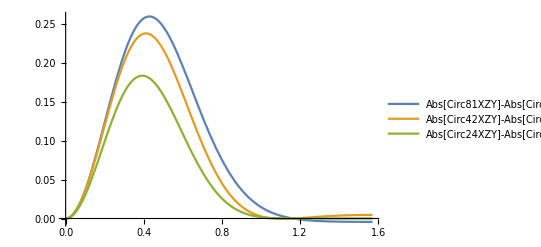

```mathematica
Plot[{Abs[Circ81XZY]-Abs[Circ82XZY],Abs[Circ42XZY]-Abs[Circ44XZY],Abs[Circ24XZY]-Abs[Circ28XZY]},{α,0,Pi/2},PlotRange->All,LabelStyle->Directive[Bold, Medium],PlotLegends->"Expressions"]
```